```mathematica
(* These are the decay rates *)
```

```mathematica
k[1]=3.1;k[2]=1;k[3]=0;k[4]=0;k[5]=0;
```

```mathematica
(* These are the initial expected numbers of nuclei *)
```

```mathematica
M0x[1]=2;M0x[2]=0.1;M0x[3]=0.001;M0x[4]=2;M0x[5]=2;
```

```mathematica
(* Initial expected numbers of decay particles *)
```

```mathematica
M0α=0.1;M0β=0.1;
```

```mathematica
Subscript[R, α,1]=1;Subscript[R, α,2]=1;Subscript[R, α,3]=0;Subscript[R, α,4]=1;Subscript[R, α,5]=1;
Subscript[R, β,1]=0;Subscript[R, β,2]=1;Subscript[R, β,3]=0;Subscript[R, β,4]=1;Subscript[R, β,5]=0;
```

```mathematica
(* Number of isotopes *)
```

```mathematica
n=3;
```

```mathematica
(* generating function solving the master equation for Poissonian intitial conditions *)
```

```mathematica
g[sα_,sβ_,s__,t_]:=Exp[M0α(sα-1)+M0β(sβ-1)+∑_(i=1)^n ((M0x[i]ⅇ^(-k[i]t)+∑_(m=1)^(i-1) M0x[m](∏_(l=m)^(i-1) k[l] sα^Subscript[R, α,l] sβ^Subscript[R, β,l])∑_(l=m)^i ⅇ^(-k[l]t)/(∏_(j=m)^i ((k[j]-k[l])+KroneckerDelta[j,l])))(s[[i]]-∏_(l=i)^(n-1) sα^Subscript[R, α,l] sβ^Subscript[R, β,l])+M0x[i](∏_(l=i)^(n-1) sα^Subscript[R, α,l] sβ^Subscript[R, β,l]-1))]
```

```mathematica
(* Maximual number of α particles in plot *)
```

```mathematica
kmax=20;
```

```mathematica
(* Simulation time in seconds *)
```

```mathematica
τmax=100;
```

```mathematica
(* Coefficients of Hermite distribution *)
```

```mathematica
aa=Table[SeriesCoefficient[Log[g[sα,1,{1,1,1},τ*0.1]],{sα,0,xk}],{xk,0,2},{τ,1,τmax}];
```

```mathematica
(* Levy-Panjer-Adelson Recursion *)
```

```mathematica
For[τ=1;p=ConstantArray[0,{kmax+1,τmax+1}],τ< τmax,τ++,For[κ=0;p[[1]][[τ+1]]=ⅇ^-1,κ<kmax,κ++,p[[κ+1+1]][[τ+1]]=1/(κ+1)∑_(j=0)^κ N[(κ+1-j)If[(κ+1-j)<3,aa[[(κ+1-j)+1]][[τ+1]],0]p[[j+1]][[τ+1]]]]]
```

```mathematica
(* For convenience, we normalize the distribution here instead of including the corresponding factors in the last recursion *)
```

```mathematica
normp=Table[p[[xk]][[τ*2]]/Sum[p[[κ2]][[τ*2]],{κ2,1,kmax}],{xk,1,kmax},{τ,2,13}];
```

```mathematica
(* Mean value for each time-step *)
```

```mathematica
meantab=Table[ ∑_(k=0)^(kmax-1) normp[[k+1]][[τ]]*k,{τ,1,12}]
```

{1.85076,2.36173,2.74074,3.02989,3.25523,3.43358,3.57629,3.69134,3.78457,3.86037,3.92215,3.97257}

```mathematica
(* Standard deviation for each time-step *)
```

```mathematica
stdtab=Table[√( ∑_(k=0)^(kmax-1) normp[[k+1]][[τ]]*k^2-∑_(k=0)^(kmax-1) normp[[k+1]][[τ]]*k),{τ,1,12}]
```

{2.00461,2.5756,3.00299,3.33071,3.58661,3.7891,3.95089,4.08103,4.18623,4.27155,4.34092,4.39742}

```mathematica
tex[string_]:=Text[Style[ToExpression[string,TeXForm,HoldForm],Large]]
```

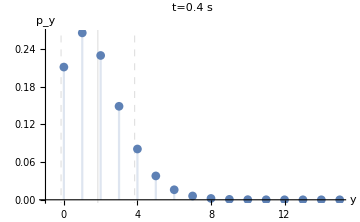
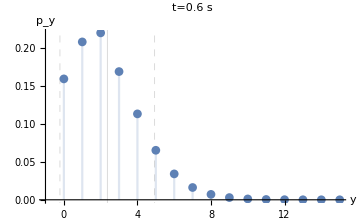
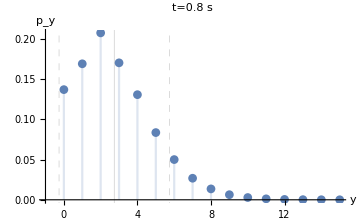
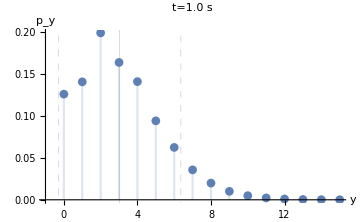
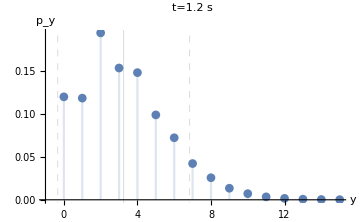
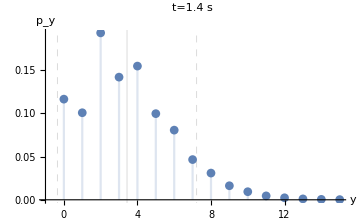
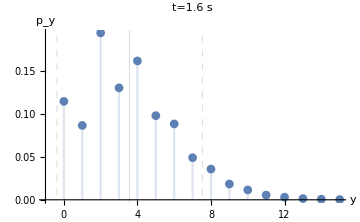
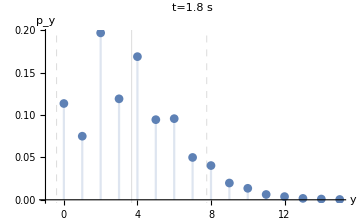

```mathematica
plottab=Table[DiscretePlot[normp[[xk+1]][[τ-1]],{xk,0,15},GridLines->{{{meantab[[τ-1]],Thick},{meantab[[τ-1]]-stdtab[[τ-1]],Dashed},{meantab[[τ-1]]+stdtab[[τ-1]],Dashed}},None},AxesLabel->{"y","p_y"},AxesOrigin->{-1,0}, PlotRange->All,ImageSize->Medium,BaseStyle->{FontSize->18},PlotMarkers->Automatic,PlotLabel->"t="<>ToString[NumberForm[τ*2*0.1,{2,1}]]<>" s"],{τ,2,13}]
```

```mathematica
For[i=1,i<=Length[plottab],i++,τ=i+1;Export[NotebookDirectory[]<>"../bilder/bateman"<>ToString[τ]<>".pdf",plottab[[i]]]]
```